## Wobbling structure in even-A nuclei

## 134Ce

### Study the wobbling quantities for 134Ce

```mathematica
ClearAll["Global`*"]
```

### Fitting parameters

```mathematica
A1isomer=0.03427331900399553;
A2isomer=0.022884383334125447;
A3isomer=0.014376941928523406;
A1deformed=0.031684938542074936;
A2deformed=0.021250218658037823;
A3deformed=0.011879240621271615;
bandhead=10;
```

### Theoretical formalism

```mathematica
omega[I_,A1_,A2_,A3_]:=2I*Sqrt[(A1-A3)(A2-A3)];
En[I_,n_,A1_,A2_,A3_]:=A3*I*(I+1)+omega[I,A1,A2,A3]*(n+1/2);
Exc[I_,n_,A1_,A2_,A3_]:=En[I,n,A1,A2,A3]-En[bandhead,0,A1,A2,A3];
```

### Experimental data (excitation energies)

```mathematica
spinsBand8={12,14,16,18,20};
spinsBand10={13,15,17};
spinsBand9={12,14,16,18,20,22};
spinsBand7={11,13,15};
energyBand8={0.799,1.554,2.657,3.569,4.343};
energyBand10={1.49,2.285,3.316};
energyBand9={0.464,1.188,2.005,2.878,3.862,4.864};
energyBand7={0.665,1.205,1.998};
```

### Graphical representations

#### Excitation Energies - Isomer

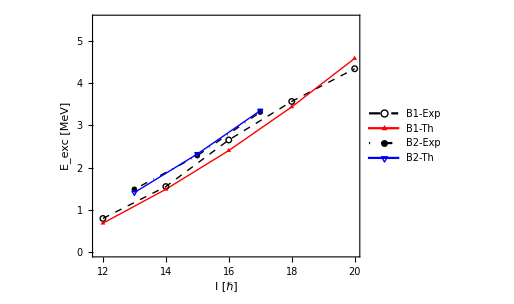

```mathematica
band8dataExp=Table[{spinsBand8[[i]],energyBand8[[i]]},{i,1,Length[spinsBand8]}];
band8dataTh=Table[{spinsBand8[[i]],Exc[spinsBand8[[i]],0,A1isomer,A2isomer,A3isomer]},{i,1,Length[spinsBand8]}];
band10dataExp=Table[{spinsBand10[[i]],energyBand10[[i]]},{i,1,Length[spinsBand10]}];
band10dataTh=Table[{spinsBand10[[i]],Exc[spinsBand10[[i]],1,A1isomer,A2isomer,A3isomer]},{i,1,Length[spinsBand10]}];
p1=ListPlot[{band8dataExp,band8dataTh},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,Joined->{True, True},PlotMarkers->{{"○",Scaled[0.045]},{"▲",Scaled[0.07]}},PlotStyle->{{Black,Dashed,Thick},{Red,Thick}},PlotRange->{Automatic,{0,5.5}},LabelStyle->{19,Bold,Black,FontFamily->"Times"},FrameLabel->{"I [ℏ]","E_exc [MeV]"},PlotLegends->Placed[{"B1-Exp","B1-Th"},{0.25,0.8}]];
p2=ListPlot[{band10dataExp,band10dataTh},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,Joined->{True, True},PlotMarkers->{{"●",Scaled[0.045]},{"▽",Scaled[0.07]}},PlotStyle->{{Black,DotDashed,Thick},{Blue,Thick}},PlotLegends->Placed[{"B2-Exp","B2-Th"},{0.8,0.25}],LabelStyle->{19,Bold,Black,FontFamily->"Times"},FrameLabel->{"I [ℏ]","E_exc [MeV]"}];
obj1=Show[p1,p2];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Wobbling-134Ce-136Nd/134Ce-excitation-isomer.pdf",obj1];
obj1
```

#### Wobbling Energies - Isomer

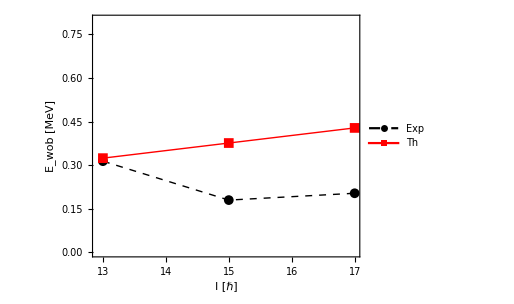

```mathematica
EwobIsomerExp=Table[{spinsBand10[[i]],energyBand10[[i]]-1/2(energyBand8[[i]]+energyBand8[[i+1]])},{i,1,Length[spinsBand10]}];
EwobIsomerTh=Table[{band10dataTh[[i,1]],band10dataTh[[i,2]]-1/2(band8dataTh[[i,2]]+band8dataTh[[i+1,2]])},{i,1,Length[band10dataTh]}];
obj2=ListPlot[{EwobIsomerExp,EwobIsomerTh},Frame->True,PlotMarkers->{Automatic, Medium},Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,Joined->{True, True},PlotStyle->{{Black,Dashed,Thick},{Red,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"Exp","Th"},{0.25,0.8}],PlotRange->{Automatic,{0,0.8}},FrameLabel->{"I [ℏ]","E_wob [MeV]"}];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Wobbling-134Ce-136Nd/134Ce-wobbling-isomer.pdf",obj2];
obj2
```

#### Excitation Energies - Deformed

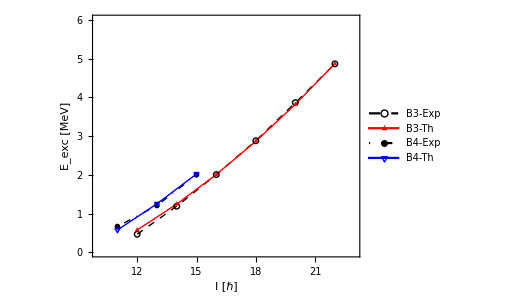

```mathematica
band9dataExp=Table[{spinsBand9[[i]],energyBand9[[i]]},{i,1,Length[spinsBand9]}];
band9dataTh=Table[{spinsBand9[[i]],Exc[spinsBand9[[i]],0,A1deformed,A2deformed,A3deformed]},{i,1,Length[spinsBand9]}];
band7dataExp=Table[{spinsBand7[[i]],energyBand7[[i]]},{i,1,Length[spinsBand7]}];
band7dataTh=Table[{spinsBand7[[i]],Exc[spinsBand7[[i]],1,A1deformed,A2deformed,A3deformed]},{i,1,Length[spinsBand7]}];
p3=ListPlot[{band9dataExp,band9dataTh},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,Joined->{True, True},PlotMarkers->{{"○",Scaled[0.045]},{"▲",Scaled[0.07]}},PlotStyle->{{Black,Dashed,Thick},{Red,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Times"},FrameLabel->{"I [ℏ]","E_exc [MeV]"},PlotLegends->Placed[{"B3-Exp","B3-Th"},{0.25,0.8}],PlotRange->{{10,23},{0,6}}];
p4=ListPlot[{band7dataExp,band7dataTh},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,Joined->{True, True},PlotMarkers->{{"●",Scaled[0.045]},{"▽",Scaled[0.07]}},PlotStyle->{{Black,DotDashed,Thick},{Blue,Thick}},PlotLegends->Placed[{"B4-Exp","B4-Th"},{0.8,0.25}],LabelStyle->{19,Bold,Black,FontFamily->"Times"},FrameLabel->{"I [ℏ]","E_exc [MeV]"}];
obj3=Show[p3,p4];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Wobbling-134Ce-136Nd/134Ce-excitation-deformed.pdf",obj3];
obj3
```

#### Wobbling Energies - Deformed

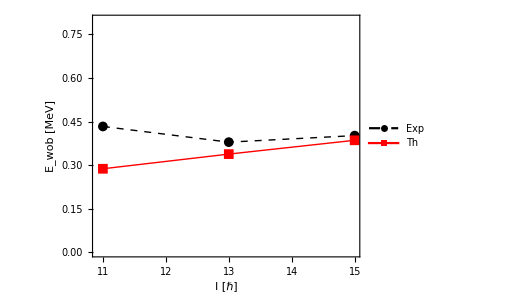

```mathematica
EwobDeformedExp=Join[{{spinsBand7[[1]],energyBand7[[1]]-1/2 energyBand9[[1]]}},Table[{spinsBand7[[i]],energyBand7[[i]]-1/2(energyBand9[[i-1]]+energyBand9[[i]])},{i,2,Length[spinsBand7]}]];
EwobDeformedTh=Join[{{spinsBand7[[1]],band7dataTh[[1,2]]-1/2 band7dataTh[[1,2]]}},Table[{spinsBand7[[i]],band7dataTh[[i,2]]-1/2(band7dataTh[[i-1,2]]+band7dataTh[[i,2]])},{i,2,Length[spinsBand7]}]];obj4=ListPlot[{EwobDeformedExp,EwobDeformedTh},Frame->True,PlotMarkers->{Automatic, Medium},Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,Joined->{True, True},PlotStyle->{{Black,Dashed,Thick},{Red,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"Exp","Th"},{0.25,0.8}],PlotRange->{Automatic,{0,0.8}},FrameLabel->{"I [ℏ]","E_wob [MeV]"}];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Wobbling-134Ce-136Nd/134Ce-wobbling-deformed.pdf",obj4];
obj4
```

## Electromagnetic transitions

```mathematica
t1[I_,A1_,A2_,A3_]:=I(A2+A1-2A3);
t2[I_,A1_,A2_]:=I(A2-A1);
w1[I_,A1_,A2_,A3_]:=(1/2(t1[I,A1,A2,A3]/(√(t1[I,A1,A2,A3]^2-t2[I,A1,A2]^2))+1))^(1/2);
w2[I_,A1_,A2_,A3_]:=(1/2(t1[I,A1,A2,A3]/(√(t1[I,A1,A2,A3]^2-t2[I,A1,A2]^2))-1))^(1/2);
Q20[Q0_,gm_]:=Q0*Cos[gm];
Q22[Q0_,gm_]:=1/(√2)Q0*Sin[gm];
BE2out[I_,Q0_,gm_,A1_,A2_,A3_]:=5/(16π)*1/I(√3 Q20[Q0,gm]*w1[I,A1,A2,A3]+√2 Q22[Q0,gm]*w2[I,A1,A2,A3])^2;
BE2in[I_,Q0_,gm_]:=5/(16π)*Q22[Q0,gm]^2;
```

```mathematica
Z=58;
A=134;
gmIsomer=-35*π/180;
beta2Isomer=0.14/0.95;
gmDeformed=25*π/180;
beta2Deformed=0.21/0.95;
Q0def[beta_]:=3/(√(5π))(1.2*A^(1/3))^2 beta*(1+0.16*beta);
```

## Isomer

```mathematica
Q0isomer=Q0def[beta2Isomer]
Q20isomer=Q20[Q0isomer,gmIsomer]
Q22isomer=Q22[Q0isomer,gmIsomer]
BE2inIsomer=BE2in[1,Q0isomer,gmIsomer]
```

4.30546

3.52683

-1.74621

0.303313

## Deformed

6.53257

5.92052

1.95217

0.379084

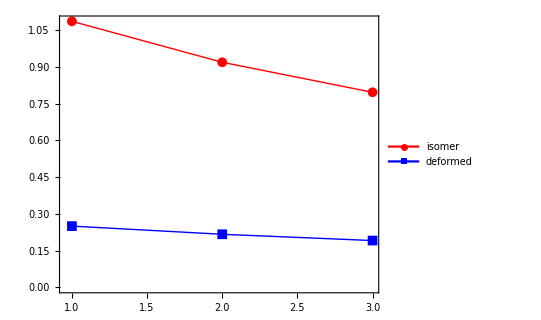

```mathematica
Q0deformed=Q0def[beta2Deformed]
Q20deformed=Q20[Q0deformed,gmDeformed]
Q22deformed=Q22[Q0deformed,gmDeformed]
BE2inDeformed=BE2in[1,Q0deformed,gmDeformed]
ListPlot[{Table[BE2out[spinsBand7[[i]],Q0deformed,gmDeformed,A1deformed,A2deformed,A3deformed],{i,1,Length[spinsBand7]}],Table[BE2out[spinsBand10[[i]],Q0isomer,gmIsomer,A1isomer,A2isomer,A3isomer],{i,1,Length[spinsBand10]}]},PlotRange->Full,Joined->True,PlotMarkers->{Automatic, Medium},PlotStyle->{{Red,Thick},{Blue,Thick}},Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,PlotLegends->Placed[{"isomer","deformed"},{0.2,0.5}]]
```

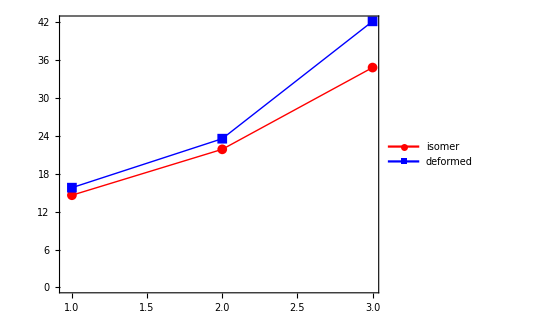

```mathematica
ListPlot[{{{1,1/(2*A1isomer)},{2,1/(2*A2isomer)},{3,1/(2A3isomer)}},{{1,1/(2A1deformed)},{2,1/(2A2deformed)},{3,1/(2A3deformed)}}},PlotMarkers->{Automatic, Medium},Joined->True,PlotRange->Full,Joined->True,PlotMarkers->{Automatic, Medium},PlotStyle->{{Red,Thick},{Blue,Thick}},Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,PlotLegends->Placed[{"isomer","deformed"},{0.2,0.7}]]
```